```mathematica
ClearAll[eqs, sol,n];
m = 9;
Subscript[γ, c]=2.4 10^11;
Subscript[γ, s]= 1.458 10^9;
Subscript[γ, n]= 3 J 10^9;
Subscript[γ, p]= 3.6 J 10^9 ;
J = 1/3; (* are you sure here ??? *)
ξ = 1/10;
Subscript[f, r]= 2.5 10^9;
τ̃ =7.45; (*5.48;*)(* 6.48;*) (*7.45*)
τ =τ̃/Subscript[f, r]; (* it is important to find right time value *)

IC = { n[t /; t< 0]==0.01, s[t /; t< 0]==1};
eqs= {
D[s[t],t] == (Subscript[γ, c] Subscript[γ, n])/(J Subscript[γ, s])n[t] (s[t] +1)-Subscript[γ, p] s[t](s[t]+1),
D[ n[t], t] == Subscript[γ, s] ξ(1+J)(1 + s[t-τ])-Subscript[γ, s] n[t] - Subscript[γ, s] J s[t] - Subscript[γ, n] n[t](1+s[t])+(Subscript[γ, s] Subscript[γ, p])/Subscript[γ, c] J s[t] (1+s[t])
};
Num = 100;
tMax =Num * τ; (*5 *) (* 50 -- characteristic time *) 
sol = NDSolve[Join[eqs, IC], {s[t], n[t]}, {t, 0., tMax}
,Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}},AccuracyGoal->60,PrecisionGoal->3,MaxSteps->Infinity]⟦1⟧
```

{s[t]→                                   -7
InterpolatingFunction[{{0., 2.98 10  }}, <>][t],n[t]→                                   -7
InterpolatingFunction[{{0., 2.98 10  }}, <>][t]}

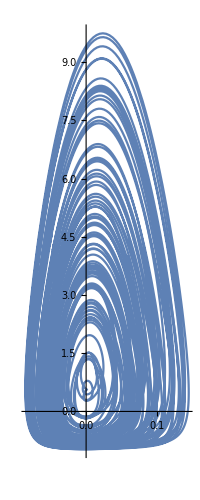

```mathematica
ParametricPlot[({n[t],s[t]}/.sol),{t,0.1tMax,0.2tMax},PlotPoints->500,PlotRange->All,AspectRatio->Full]
```

```mathematica
s[t]/.sol /. {t -> t - 0.01τ}
```

-7
InterpolatingFunction[{{0., 2.98 10  }}, <>][-2.98×10^-11+t]

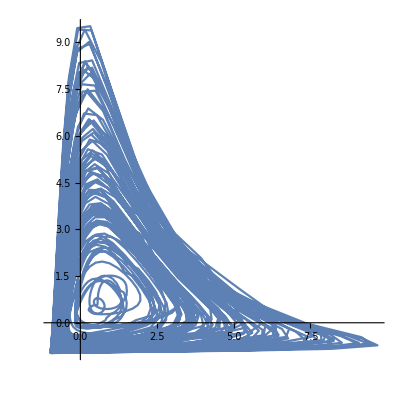

```mathematica
Sfunc = s[t]/.sol;
(*Y = s[t] /. sol /. {t -> t-τ/45};*)
(*ParametricPlot[{X,Y},{t,0.1tMax,0.2tMax },PlotRange->All,AspectRatio->Full]*)
```

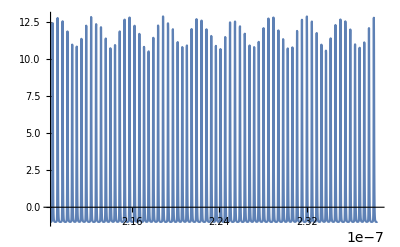

```mathematica
Plot[X, {t, 0.7tMax, 0.8tMax}, PlotRange->All]
```

```mathematica
x = Range[0.7tMax, 0.8tMax, τ/10];
y = Map[X, x];
```

```mathematica
data = Transpose@Join[{x}, {y}];
ListPlot[data]
```